```mathematica
(*For some reason this function runs really fast.*)
```

```mathematica
points[a_,b_,n_]:=N[Array[a+(b-a) #/n&,n+1,0],MachinePrecision]
conpoints[a_,n_]:=ConstantArray[a,n+1]
Npoints = 15;
nsmax = 0.962514+0.00406408;
nsmin = 0.962514-0.00406408;
rlim = 0.064;
Print["A total of ",(Npoints+1)^5, " points will be checked"]
```

A total of 1048576 points will be checked

```mathematica
Clear[viable,nsviable,results,rresults,inputs];
listN=points[50,60,Npoints];
listk=points[0.4,0.9,Npoints];
listb=points[14,15,Npoints];
listc1=conpoints[1,Npoints];
listp = points[14,15,Npoints];
inputs=Tuples[{listN,listk,listb,listp,listc1}];
results=N[ParallelMap[nSfinal@@#&,inputs],13];
nsviable=Flatten[Reap[Do[If[nsmin<results[[i]]<nsmax,Sow[inputs[[i]]]],{i,Length[results]}]][[2]],1];
rresults=ParallelMap[rfinal@@#&,nsviable];viable=Flatten[Reap[Do[If[rresults[[i]]<rlim,Sow[nsviable[[i]]]],{i,Length[nsviable]}]][[2]],1];
```

```mathematica
(*N,k,b,c1,c2 . k<0 , b>0 , b>>>-k*)
```

2000000000000

```mathematica
N[viable[[1]],20]
N1=52;
l=0.4;
o =14.4;
p1=14;
Quiet[N[nSfinal[N1,l,o,p1,1],15]]
Quiet[N[rfinal[N1,l,o,p1,1],15]]
```

{52.,0.4,14.4,14.,1.}

0.961741

0.00547795

```mathematica
viable = Import["C:\\Users\\grega\\Documents\\viable-ns-parameters-emergent-universe.mx"](*If you already have viabla inputs , and want to import them*)
```

{{50.,0.433333,14.8667,14.4667,1},1886,{60.,0.6,14.6,14.5333,1}}
 |  |  |  |

```mathematica
ntresults=N[ParallelMap[nTfinal@@#&,viable],MachinePrecision];
```

```mathematica
nSarr = N[ParallelMap[nSfinal@@#&,viable],MachinePrecision]
rarr = N[ParallelMap[rfinal@@#&,viable],MachinePrecision]
Length[nSarr]
Length[viable]
```

{0.966025,0.966025,0.966025,0.966025,0.966025,0.966025,0.966025,0.966025,0.966025,1871,0.966298+0. ⅈ,0.966298+0. ⅈ,0.966298+0. ⅈ,0.966298+0. ⅈ,0.966298+0. ⅈ,0.966298+0. ⅈ,0.966298+0. ⅈ,0.966298+0. ⅈ}
 |  |  |  |

{0.00410616,0.00410616,0.00410616,0.00410616,0.00410616,0.00410616,0.00410616,0.00410616,1872,0.00966615+0. ⅈ,0.00966615+0. ⅈ,0.00966615+0. ⅈ,0.00966615+0. ⅈ,0.00966615+0. ⅈ,0.00966615+0. ⅈ,0.00966615+0. ⅈ,0.00966615+0. ⅈ}
 |  |  |  |

1888

1888

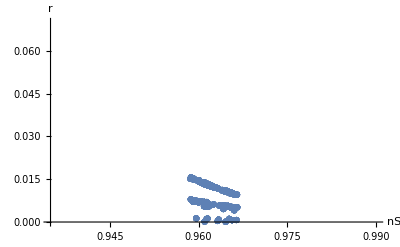

```mathematica
plot1 = ListPlot[Transpose[{nSarr,rarr}],PlotRange->{{0.935,0.99},{0,0.07}},AxesLabel->{"nS","r"},PlotStyle->PointSize[0.011]]
```